# GCCH PHAT

## ...

### Introduction

Accurately estimating the direction of arrival (DOA) of sound sources is essential in various applications, including audio beamforming, speech recognition, and source localization. One popular algorithm for DOA estimation is the Generalized Cross-Correlation Phase Transform (GCC-PHAT) algorithm. In this blog post, we will explore the implementation of the GCC-PHAT algorithm using Wolfram Mathematica.

### Understanding the GCC - PHAT Algorithm

The GCC - PHAT algorithm leverages the cross - correlation of microphone signals to estimate the time difference of arrival (TDOA) between the microphones.By calculating the phase transform of the cross - correlation, it provides DOA estimates.

### Preparing the Audio Signals

Before implementing the GCC-PHAT algorithm, we need to ensure that the audio signals from the microphones are preprocessed. In order to ensure proper preprocessing, I generated a directional sound source. Specifically, I simulated a person speaking at an angle of 45 degrees. To achieve this, I imported a clean mono-channel audio signal and convolved it with the Room Impulse Response (RIR). This process emulates the directional characteristics of sound propagation. Afterwards, I utilized Mathematica to import the directional audio sound source and conducted additional steps to verify the integrity of the data.

```mathematica
directionalAudio = Import["C:/Users/janar/Desktop/wolfram career/output.wav","Audio"]
```

```mathematica
fs =QuantityMagnitude[AudioSampleRate[directionalAudio]]
```

16000

```mathematica
AudioChannels[directionalAudio]
```

2

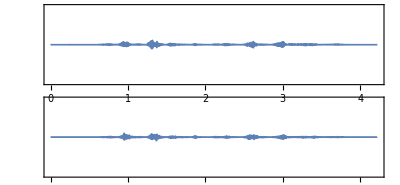

```mathematica
AudioPlot[directionalAudio]
```

### Separating the audio file into two channels

After importing the input source, we need to separate the two channels as follows

```mathematica
s1 =AudioChannelSeparate[directionalAudio,1]
```

```mathematica
s2 =AudioChannelSeparate[directionalAudio,2]
```

### Calculating the FFT

Now, we need to calculate the Fourier transform for each channel and consider one of them (lets say the first channel) as a reference. We start by extracting the audio data to be able to calculate FFT. Then, we print the dimension and plot the output of this step.

```mathematica
data1=AudioData[s1];
```

```mathematica
Dimensions[data1]
```

{1,67583}

```mathematica
data2= AudioData[s2];
```

```mathematica
Dimensions[data2]
```

{1,67583}

```mathematica
s1FFT= Fourier[data1];
```

```mathematica
Dimensions[s1FFT]
```

{1,67583}

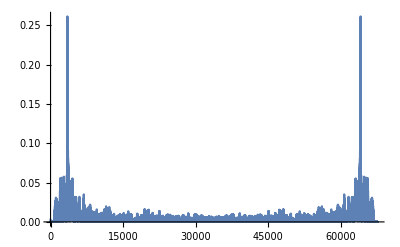

```mathematica
ListLinePlot[Abs[s1FFT], PlotRange->All]
```

```mathematica
s2FFT= Fourier[data2];
```

```mathematica
Dimensions[s2FFT]
```

{1,67583}

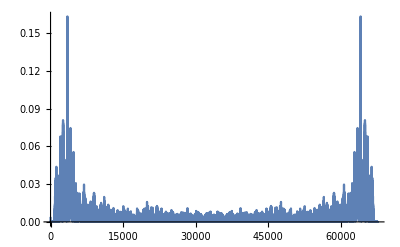

```mathematica
ListLinePlot[Abs[s2FFT], PlotRange->All]
```

### Calculating Power Spectrum Density

Next, we need to compute of spectra S_i1 (t, f) and S_i2 (t, f) through Fourier transforms applied to windowed segments of S_i1 and S_i2 , centered around time instant t. Then, these spectra are used to estimate the normalized cross power-spectrum:

ϕ(i (t,f) = (S_i1(t,f) S_i2^* (t,f))/(|S_i1(t,f)| |S_i2 (t,f)|)

Here, we start by calculating the numerator of the equation

```mathematica
r=s2FFT*Conjugate[s1FFT];
```

```mathematica
Dimensions[r]
```

{1,67583}

Then, We compute the normalized cross power - spectrum

```mathematica
cspNorm = r/Abs[r];
```

```mathematica
Dimensions[cspNorm]
```

{1,67583}

Now, we need to compute the inverse Fourier transform of ϕ_i(t, f):

C_i(t,τ) = ∫_(-∞)^(+∞) ϕ_i(t,f) e^j2πfτ ⅆf

Here, we apply the IFT

```mathematica
cc=Flatten@Re[InverseFourier[cspNorm]];
```

```mathematica
Dimensions[cc]
```

{67583}

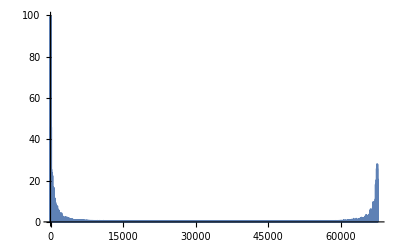

```mathematica
ListLinePlot[Abs[cc], PlotRange->All]
```

```mathematica
Ceiling[Length[cc]/2]
```

33792

And here we swap the left and right parts

```mathematica
cc2= RotateLeft[cc,Ceiling[Length[cc]/2]];
```

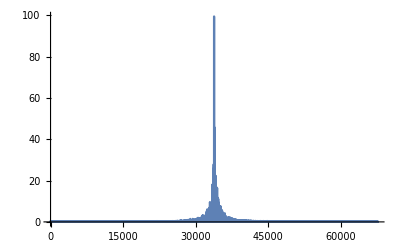

```mathematica
ListLinePlot[Abs[cc2], PlotRange->All]
```

We find the index of the Signal’s center

```mathematica
idxCenter = Floor[(n/2+1)/2]
```

33792

Each delay estimate δ_i^^between microphones of the i_th pair is computed by maximizing the corresponding CM integration

δ_i^^  = argmax∫C_i(t,τ)ⅆt

```mathematica
idxTau=FirstPosition[Abs@cc2,Max[Abs@cc2]] - idxCenter
```

{17}

We convert the samples to seconds

```mathematica
tau = N[idxTau/fs]
```

{0.0010625}

We need to define the sound velocity and the distance between the two microphones, in order to use them in the equation that calculate the estimated angle

```mathematica
c=340;
```

```mathematica
d=0.5;
```

```mathematica
phiEst= ArcCos[c*tau/d]*180/π
```

{43.7387}

Finally, we got the estimated angle = 43.7 which is close to the real angle we were trying to estimate in this blog = 45.  2degrees error is often considered good enough for practical purposes because the resolution of the human auditory system for localizing sound sources is coarser than this. Therefore, a 1-degree error is well within the range  of what humans can perceive.